## Data:

## First Iteration

```mathematica
redistbets="data";
```

```mathematica
notTimedRedistributiveFirstIteration="data";
timedRedistributiveFirstIteration="data";
choicesRedistributive=Join[timedRedistributiveFirstIteration,notTimedRedistributiveFirstIteration]/100;
```

## Second Iteration

```mathematica
notTimedRedistributiveSecondIteration="data";
timedRedistributiveSecondIteration="data";
choicesRedistributive=Join[timedRedistributiveSecondIteration,notTimedRedistributiveSecondIteration]/100;
```

## time data

```mathematica
timingsFirstIteration="data";
```

```mathematica
timingsSecondIteration="data";
```

## Analysis of Timings

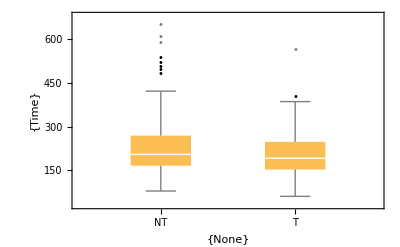

```mathematica
times=timingsFirstIteration;
notTimedTime=times[[2;;Length[times],1]]//.""->Sequence[];
timedTime=times[[2;;Length[times],2]];
movingAvg=ArrayPad[MovingAverage[notTimedTime,5],{5-1,0},"Fixed"];
subtractedmean=(Subtract@@@Transpose[{notTimedTime,movingAvg}]);
outpos=Position[subtractedmean,x_/;x>StandardDeviation[subtractedmean]*3];
Length[outpos];
notTimedTime=Delete[notTimedTime,outpos];
movingAvg=ArrayPad[MovingAverage[timedTime,5],{5-1,0},"Fixed"];
subtractedmean=(Subtract@@@Transpose[{timedTime,movingAvg}]);
outpos=Position[subtractedmean,x_/;x>StandardDeviation[subtractedmean]*3];
Length[outpos];
timedTime=Delete[timedTime,outpos];
BoxWhiskerChart[{notTimedTime,timedTime},"Outliers",ChartLabels->{{"NT","T"}},AxesLabel->{{None},{"Time"}},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12]]
```

## Optimal Tau Calculation + Figure

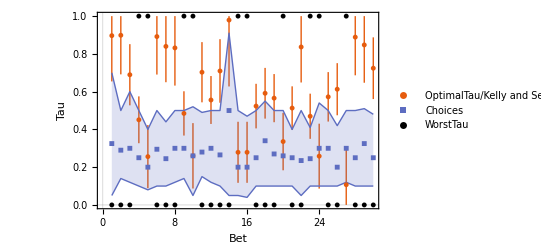

```mathematica
respondentsQuant={#[[1]],{#[[2]],#[[3]]}}&/@Transpose[{Median[choicesRedistributive],Median[choicesRedistributive]-Quantile[choicesRedistributive,1/4],Quantile[choicesRedistributive,3/4]-Median[choicesRedistributive]}];
respondentsQuantAround=Around@@@(respondentsQuant);
bets=redistbets;
optimalTau=List[];
worstTau=List[];
kellyTau=List[];
Exlist=List[];
For [i=1,i≤Length[redistbets],i++,
r1=Max[bets[[i,1,2]],bets[[i,2,2]]];
r2=Min[bets[[i,1,2]],bets[[i,2,2]]];
p=bets[[i,1,1]];
tau=(r1-r1*r2+p*r2-p*r1)/(r1+r2-1-r1*r2);
kelly=1-(p/Abs[r2-1]-p/(r1-1));
AppendTo[worstTau,If[Log[(r1*r2)^p]+1>1,1,0]];
outcome=Log[((r1+(1-r1)tau)(r2+(1-r2)tau))^p]+1;
delta=Exp[outcome-1]-If[(r1*r2)^p<1,(r1*r2)^p,1];
EX=(r1+r2)/2;
AppendTo[Exlist,EX];
error=0.95;
bound=Exp[(outcome-(Min[Log[(r1*r2)^p]+1,1]))error+Min[Log[(r1*r2)^p]+1,1]-1];
discrimantError=(r1-2*r1*r2+r2)^2-4*(r1*r2-bound^2)(1+r1*r2-r1-r2);
upperbound=(-(r1-2*r1*r2+r2)-Sqrt[discrimantError])/(2*(1+r1*r2-r1-r2));
lowerbound=(-(r1-2*r1*r2+r2)+Sqrt[discrimantError])/(2*(1+r1*r2-r1-r2));
AppendTo[optimalTau,Around[N[tau],{If[lowerbound<0,0-N[tau],lowerbound-N[tau]],If[upperbound>1,1-N[tau],upperbound-N[tau]]}]];
]
tauoverviewplot50Original=Show[ListPlot[{optimalTau,respondentsQuantAround},IntervalMarkers->{"Fences","Bands"},FrameLabel->{"Bet","Tau"},PlotLegends->{"OptimalTau/Kelly and Sensitivity","Choices"},PlotTheme->"Scientific",LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12],PlotMarkers->{Automatic,5}],ListPlot[worstTau,PlotStyle->Black,PlotLegends->{"WorstTau"},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12],PlotMarkers->{Automatic,5}] ]
(*keuzematrixredistT=Join[{optimalTau},timedRedistributive/100];
keuzematrixredistT=SortBy[Transpose[keuzematrixredistT],First];
keuzematrixredistNT=Join[{optimalTau},notTimedRedistributive/100];
keuzematrixredistNT=SortBy[Transpose[keuzematrixredistNT],First];
keuzematrixredist=Join[{optimalTau},choicesRedistributive];
keuzematrixredist=SortBy[Transpose[keuzematrixredist],First][[All,1;;]];*)
```

## Distances Figure

```mathematica
bets=redistbets;
distancesT=List[];
distancesNT=List[];
distancesOriginal=List[];
distanceTau=List[];
For[i=1,i≤Length[bets],i++,
r1=Max[bets[[i,1,2]],bets[[i,2,2]]];
r2=Min[bets[[i,1,2]],bets[[i,2,2]]];
p=bets[[i,1,1]];
tau=(r1-r1*r2+p*r2-p*r1)/(r1+r2-1-r1*r2);
maxOutcome=Log[((r1+(1-r1)tau)(r2+(1-r2)tau))^p]+1;
minOutcome=Log[Min[(r1*r2)^p,1]]+1;
absoluteDistance=((r1+(1-r1)tau)(r2+(1-r2)tau))^p-Min[(r1*r2)^p,1];
averageOutcome=(maxOutcome+minOutcome)/2;
distanceBetT=List[];
For[j=1,j<=Length[timedRedistributive],j++,
chooseTau=timedRedistributive[[j,i]]/100;
chooseOutcome=Log[((r1+(1-r1)chooseTau)(r2+(1-r2)chooseTau))^p]+1;
distanceT=(chooseOutcome-minOutcome)/(maxOutcome-minOutcome);
;
AppendTo[distanceBetT,distanceT];
];
distanceBetNT=List[];
For[j=1,j<=Length[notTimedRedistributive],j++,
chooseTau=notTimedRedistributive[[j,i]]/100;
chooseOutcome=Log[((r1+(1-r1)chooseTau)(r2+(1-r2)chooseTau))^p]+1;
distanceNT=(chooseOutcome-minOutcome)/(maxOutcome-minOutcome);
AppendTo[distanceBetNT,distanceNT];
];
distanceBet=List[];
For[j=1,j<=Length[choicesRedistributive],j++,
chooseTau=choicesRedistributive[[j,i]];
chooseOutcome=Log[((r1+(1-r1)chooseTau)(r2+(1-r2)chooseTau))^p]+1;
distance=(chooseOutcome-minOutcome)/(maxOutcome-minOutcome);
deltaTau=optimalTau[[i,1]]-chooseTau;
AppendTo[distanceBet,distance];
AppendTo[distanceTau,{absoluteDistance,deltaTau}]
];
AppendTo[distancesNT,distanceBetNT];
AppendTo[distancesT,distanceBetT];
AppendTo[distancesOriginal,distanceBet]
]
```

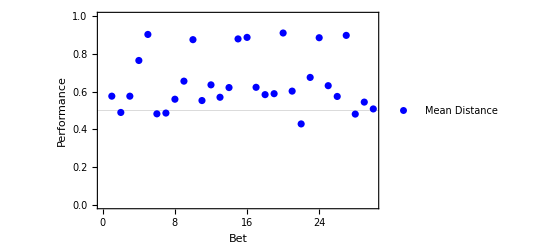

```mathematica
ListPlot[Mean[Transpose[distancesOriginal]](*{Median[Transpose[distancesNT]],Median[Transpose[distancesT]],Median[Transpose[distances]]}*),PlotStyle->{Blue(*,Red,Black*)},PlotLegends->{(*"NotTimed","Timed",*)"Mean Distance"},GridLines->{{},{0.5}},FrameLabel->{"Bet","Performance"},PlotTheme->"Scientific",LabelStyle->LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12],PlotRange->{Automatic,{0,1}}]
```

## Growth Figure, Respondents and Synthetic Agents

```mathematica
growthRatesM=List[];
growthRatesR=List[];
growthRatesNR=List[];
growthRatesOR=List[];
GrowthRespondent=List[];
For[i=1,i≤Length[choicesRedistributive],i++,
rate=1;
rateR=1;
rateNR=1;
rateOR=1;
ratesR={1};
ratesNR={1};
ratesOR={1};
For[j=1,j≤ 30 ,j++,
rateR=rateR*(redistbets[[j,altrandomR[[j]],2]]+(1-redistbets[[j,altrandomR[[j]],2]])(choicesRedistributive[[i,j]]));
rateNR=rateNR*redistbets[[j,altrandomR[[j]],2]];
rateOR=rateOR*(redistbets[[j,altrandomR[[j]],2]]+(1-redistbets[[j,altrandomR[[j]],2]])(optimalTau[[j]]["Value"]));
AppendTo[ratesNR,rateNR];
AppendTo[ratesR,rateR];
AppendTo[ratesOR,rateOR];
];
AppendTo[growthRatesOR,ratesOR];
AppendTo[growthRatesR,ratesR];
AppendTo[GrowthRespondent,Prepend[ratesR,choicesRedistributive[[i,1]]]];
AppendTo[growthRatesNR,ratesNR];
]
```

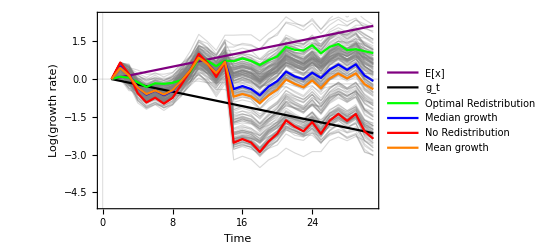

```mathematica
respondentsRedistributonPlot=Show[ListLinePlot[Log[growthRatesR],PlotRange->{Automatic,{-5,2.5}},PlotTheme->"Scientific",PlotStyle->Directive[Opacity[0.3],{Gray},Thickness[0.002]],FrameLabel->{"Time","Log(growth rate)"},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12]],Plot[Log[Mean[1/2*redistbets[[All,1,2]]+1/2*redistbets[[All,2,2]]]](x-1),{x,1,31},PlotRange->{Automatic,{-5,2.5}},PlotStyle->{Purple},PlotTheme->"Scientific",PlotLegends->{"E[x]"},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12]],Plot[Mean[1/2*Log[redistbets[[All,1,2]]]+1/2*Log[redistbets[[All,2,2]]]](x-1),{x,1,31},PlotStyle->{Black},PlotTheme->"Scientific",PlotLegends->{"g_t"},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12]],ListLinePlot[Log[growthRatesOR[[2]]],PlotStyle->{Green},PlotTheme->"Scientific",PlotLegends->{"Optimal Redistribution"},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12]],
ListLinePlot[Median[Log[growthRatesR]],PlotRange->{Automatic,{-5,2.5}},PlotTheme->"Scientific",PlotStyle->{Blue},PlotLegends->{"Median growth"},LabelStyle->Directive["Arial",Black,FontSize->12]],
ListLinePlot[Log[growthRatesNR[[2]]],PlotStyle->{Red},PlotTheme->"Scientific",PlotLegends->{"No Redistribution"},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12]],ListLinePlot[Mean[Log[growthRatesR]],PlotRange->{Automatic,{-5,2.5}},PlotTheme->"Scientific",PlotStyle->{Orange},PlotLegends->{"Mean growth"},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12]]]
```